```mathematica
<<VilCretas`
```

VilCretas está disponible.

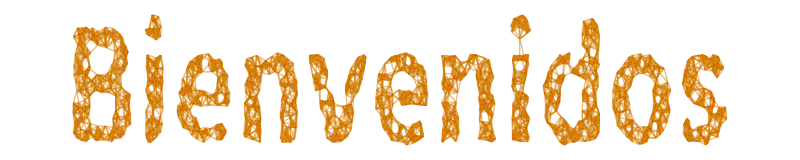

```mathematica
GrafoString["Bienvenidos"]
```

```mathematica
A={75,3,29,60,9,11,91};
MR=({{0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {1, 1, 1, 0, 1, 1, 1}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}});
```

```mathematica
R=RelBinMatriz[MR, A,A]
ClasificacionRelBin[R,A]
```

{{3,60},{9,60},{11,60},{29,60},{60,3},{60,9},{60,11},{60,29},{60,75},{60,91},{75,60},{91,60}}

{False,True,False,False}

```mathematica
?ClasificacionRelBin
```

```mathematica
A=Range[20];
R=RelBin["a^3-b^3>=96&&Mod[a+b,11]==0",A,A]
```

{{7,4},{8,3},{9,2},{10,1},{12,10},{13,9},{14,8},{15,7},{16,6},{17,5},{17,16},{18,4},{18,15},{19,3},{19,14},{20,2},{20,13}}

```mathematica
DominioRelBin[R]
```

{7,8,9,10,12,13,14,15,16,17,18,19,20}

```mathematica
{DominioRelBin[R]//Length, Length[DominioRelBin[R]]}
```

{13,13}

```mathematica
A={48,13,4,32,14,45,41,10,31,21,9,16,12,24,26,29,35,19,27,43};
B={34,12,3,10,6,2,40,36,15,50,17,8,30,19,49,32,28,41,26,43};
```

```mathematica
R=RelBin["GCD[a,b]>=5",A,B]
```

{{48,12},{48,6},{48,40},{48,36},{48,8},{48,30},{48,32},{13,26},{32,40},{32,8},{32,32},{14,49},{14,28},{45,10},{45,40},{45,36},{45,15},{45,50},{45,30},{41,41},{10,10},{10,40},{10,15},{10,50},{10,30},{21,49},{21,28},{9,36},{16,40},{16,8},{16,32},{12,12},{12,6},{12,36},{12,30},{24,12},{24,6},{24,40},{24,36},{24,8},{24,30},{24,32},{26,26},{35,10},{35,40},{35,15},{35,50},{35,30},{35,49},{35,28},{19,19},{27,36},{43,43}}

```mathematica
?MatrizRelBin
```

```mathematica
MatrizRelBin[R,A,B, encabezados->True]
```

| 34 | 12 | 3 | 10 | 6 | 2 | 40 | 36 | 15 | 50 | 17 | 8 | 30 | 19 | 49 | 32 | 28 | 41 | 26 | 43
48 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
32 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
45 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
41 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
10 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
31 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
12 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
26 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
35 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
43 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

```mathematica
ElementRelBinQ[R,{35,28}]
```

True

```mathematica
Length[R]
```

53

```mathematica
opciones={{1,2},{35,28}};
Table[i->ElementRelBinQ[R,i],{i,opciones}]
```

{{1,2}→False,{35,28}→True}

```mathematica
GCD[a,b]>=5
```

```mathematica
A={93,90,5,54,55,25};
R={{90,5},{54,90},{54,54},{54,25},{54,93},{54,5},{5,5},{5,54},{5,55},{5,25},{55,55},{55,25},{93,25},{25,90},{54,93},{25,5}};
R//Length
```

16

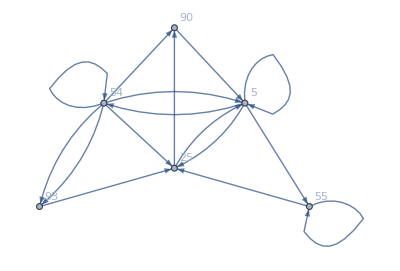

```mathematica
Grafo[R,dirigido->True](*OPCIONAL*)
```

```mathematica
MatrizRelBin[R,A,A]
```

(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0 | 0)

```mathematica
MatrizRelBin[R,A,A,encabezados->True]
```

| 93 | 90 | 5 | 54 | 55 | 25
93 | 0 | 0 | 0 | 0 | 0 | 1
90 | 0 | 0 | 1 | 0 | 0 | 0
5 | 0 | 0 | 1 | 1 | 1 | 1
54 | 1 | 1 | 1 | 1 | 0 | 1
55 | 0 | 0 | 0 | 0 | 1 | 1
25 | 0 | 1 | 1 | 0 | 0 | 0

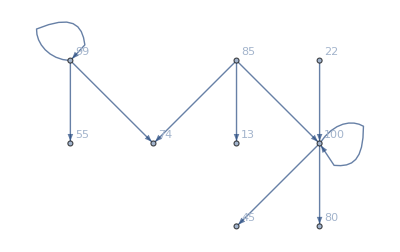

```mathematica
R={{99,99},{99,55},{99,74},{85,74},{85,13},{85,100},{22,100},{100,100},{100,45},{100,80}};
Grafo[R,dirigido->True](*Opcional*)
```

```mathematica
opcion1={{99,55},{85,13},{99,74},{85,100},{22,100},{100,45},{85,74},{99,99},{100,100},{100,80}};
Table[i->ElementRelBinQ[opcion1,i],{i,R}]
Length[R]==Length[opcion1]
Table[i->ElementRelBinQ[R,i],{i, opcion1}]
```

{{99,99}→True,{99,55}→True,{99,74}→True,{85,74}→True,{85,13}→True,{85,100}→True,{22,100}→True,{100,100}→True,{100,45}→True,{100,80}→True}

True

{{99,55}→True,{85,13}→True,{99,74}→True,{85,100}→True,{22,100}→True,{100,45}→True,{85,74}→True,{99,99}→True,{100,100}→True,{100,80}→True}

```mathematica
opcion2={{99,55},{13,85},{99,74},{85,100},{22,100},{100,45},{85,74},{99,99},{100,100},{100,80}};
Table[i->ElementRelBinQ[opcion2,i],{i,R}]
Length[R]==Length[opcion2]
Table[i->ElementRelBinQ[R, i],{i,opcion2}]
```

{{99,99}→True,{99,55}→True,{99,74}→True,{85,74}→True,{85,13}→False,{85,100}→True,{22,100}→True,{100,100}→True,{100,45}→True,{100,80}→True}

True

{{99,55}→True,{13,85}→False,{99,74}→True,{85,100}→True,{22,100}→True,{100,45}→True,{85,74}→True,{99,99}→True,{100,100}→True,{100,80}→True}

```mathematica
opcion3={{99,55},{13,13},{99,74},{85,100},{22,100},{100,45},{85,74},{99,99},{100,100},{100,80}};
Table[i->ElementRelBinQ[opcion3,i],{i,R}]
Length[R]==Length[opcion3]
Table[i->ElementRelBinQ[R, i],{i,opcion3}]
```

{{99,99}→True,{99,55}→True,{99,74}→True,{85,74}→True,{85,13}→False,{85,100}→True,{22,100}→True,{100,100}→True,{100,45}→True,{100,80}→True}

True

{{99,55}→True,{13,13}→False,{99,74}→True,{85,100}→True,{22,100}→True,{100,45}→True,{85,74}→True,{99,99}→True,{100,100}→True,{100,80}→True}

```mathematica
opcion4={{99,55},{85,13},{99,74},{85,100},{22,100},{100,45},{85,74},{99,99},{100,100},{80,80}};
Table[i->ElementRelBinQ[opcion4,i],{i,R}]
Length[R]==Length[opcion4]
Table[i->ElementRelBinQ[R, i],{i,opcion4}]
```

{{99,99}→True,{99,55}→True,{99,74}→True,{85,74}→True,{85,13}→True,{85,100}→True,{22,100}→True,{100,100}→True,{100,45}→True,{100,80}→False}

True

{{99,55}→True,{85,13}→True,{99,74}→True,{85,100}→True,{22,100}→True,{100,45}→True,{85,74}→True,{99,99}→True,{100,100}→True,{80,80}→False}

```mathematica
A=Range[-5,1000,3];
B=Range[5,998,3];
```

```mathematica
PC[A,B]//Length
```

111552

Si solicitan el dominio A x B

```mathematica
DominioRelBin[PC[A,B]]//Length
```

336

```mathematica
A=Range[20];
R=RelBin["Mod[a^2+b^2,2]!=0&&a^3-b^3<=41",A,A]
Length[R]
DominioRelBin[R]
Length[DominioRelBin[R]]
```

{{1,2},{1,4},{1,6},{1,8},{1,10},{1,12},{1,14},{1,16},{1,18},{1,20},{2,1},{2,3},{2,5},{2,7},{2,9},{2,11},{2,13},{2,15},{2,17},{2,19},{3,2},{3,4},{3,6},{3,8},{3,10},{3,12},{3,14},{3,16},{3,18},{3,20},{4,3},{4,5},{4,7},{4,9},{4,11},{4,13},{4,15},{4,17},{4,19},{5,6},{5,8},{5,10},{5,12},{5,14},{5,16},{5,18},{5,20},{6,7},{6,9},{6,11},{6,13},{6,15},{6,17},{6,19},{7,8},{7,10},{7,12},{7,14},{7,16},{7,18},{7,20},{8,9},{8,11},{8,13},{8,15},{8,17},{8,19},{9,10},{9,12},{9,14},{9,16},{9,18},{9,20},{10,11},{10,13},{10,15},{10,17},{10,19},{11,12},{11,14},{11,16},{11,18},{11,20},{12,13},{12,15},{12,17},{12,19},{13,14},{13,16},{13,18},{13,20},{14,15},{14,17},{14,19},{15,16},{15,18},{15,20},{16,17},{16,19},{17,18},{17,20},{18,19},{19,20}}

103

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

19

```mathematica
OddQ[3]
```

True

```mathematica
A={0,4,5,7,9,10,12,13,16,19};
B={0,1,2,3,5,12,15,16};
H={1,4,9,13,14,17,18,19,21,22,23,24};
R1={{0,0},{5,5},{5,12},{12,0},{16,16}};
R2={{0,18},{0,24},{5,17},{12,19},{16,23}};
MR1=MatrizRelBin[R1,A,B][[1]];
MR2=MatrizRelBin[R2,B,H][[1]];
```

```mathematica
R=RelBinMatriz[ProductoBooleano[MR1, MR2][[1]],A,H]
```

{{0,18},{0,24},{5,17},{5,19},{12,18},{12,24},{16,23}}

```mathematica
R=RelacionComposicion[R2,R1]
```

{{0,18},{0,24},{5,17},{5,19},{12,18},{12,24},{16,23}}

```mathematica
opciones={{4,21},{10,24},{0,24},{7,21},{0,18},{5,17}};
Table[i->ElementRelBinQ[R,i],{i, opciones}]
```

{{4,21}→False,{10,24}→False,{0,24}→True,{7,21}→False,{0,18}→True,{5,17}→True}

```mathematica
A={44,62,24,98,85,43,68,35,69,77};
R=RelBin["Mod[a^2-b^2,5]==0",A,A]
```

{{44,44},{44,24},{44,69},{62,62},{62,98},{62,43},{62,68},{62,77},{24,44},{24,24},{24,69},{98,62},{98,98},{98,43},{98,68},{98,77},{85,85},{85,35},{43,62},{43,98},{43,43},{43,68},{43,77},{68,62},{68,98},{68,43},{68,68},{68,77},{35,85},{35,35},{69,44},{69,24},{69,69},{77,62},{77,98},{77,43},{77,68},{77,77}}

```mathematica
ClasesEquivalencia[R,A]
```

[44]={44,24,69}

[62]={62,98,43,68,77}

[24]={44,24,69}

[98]={62,98,43,68,77}

[85]={85,35}

[43]={62,98,43,68,77}

[68]={62,98,43,68,77}

[35]={85,35}

[69]={44,24,69}

[77]={62,98,43,68,77}

El conjunto de clases de equivalencia distintas es:

{{44,24,69},{62,98,43,68,77},{85,35}}

```mathematica
A={29,18,1,65,68,69,12,17,59,23,32,21,49,38,2};
R=RelBin["Mod[a^2-1,b^2-1]==0",A,A]
```

{{29,29},{29,2},{18,18},{1,29},{1,18},{1,65},{1,68},{1,69},{1,12},{1,17},{1,59},{1,23},{1,32},{1,21},{1,49},{1,38},{1,2},{65,65},{65,23},{65,2},{68,68},{68,2},{69,69},{12,12},{17,17},{17,2},{59,59},{59,2},{23,23},{23,2},{32,32},{32,2},{21,21},{49,49},{49,2},{38,38},{38,2},{2,2}}

```mathematica
ClasificacionRelBin[R,A]
```

{False,False,True,True}

```mathematica
?ClasificacionRelBin
```

```mathematica
ClasesEquivalencia[R,A]
```